```mathematica
u[x_,y_,t_,d_]:=1/(4*Pi*t*Det[d])*Exp[-(Transpose[{x,y}].Inverse[d].{x,y})/(4*t)];
d10={{0.488,-0.086},{-0.086,0.016}};
d45={{0.283,-0.252},{-0.252,0.283}};
d22={{0.431,-0.178},{-0.178,0.074}};
```

```mathematica
data10={Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N20_theta10\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N40_theta10\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N80_theta10\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N160_theta10\\final.csv"]};

data22={Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N20_theta22\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N40_theta22\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N80_theta22\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N160_theta22\\final.csv"]};

data45={Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N20_theta45\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N40_theta45\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N80_theta45\\final.csv"],Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N160_theta45\\final.csv"]};
dataAll={data10,data22,data45}[[All,All,2;;-2]];
Ns={20,40,80,160};
thetas={10,22.5,45};
```

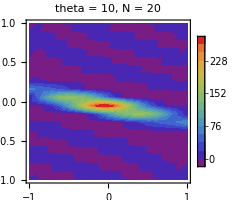
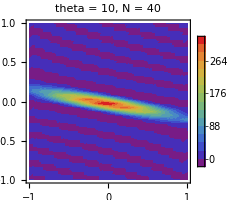
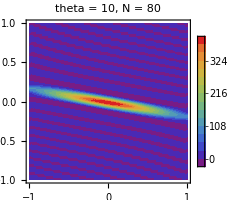
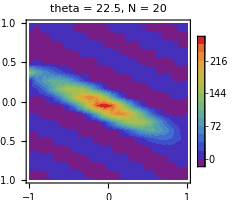
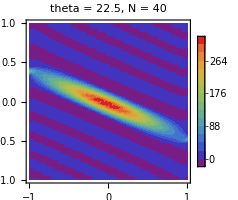
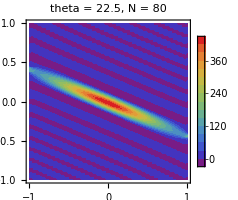
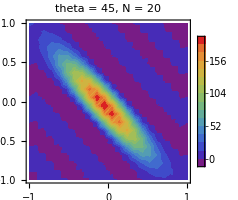
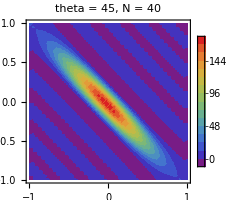
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ListContourPlot[dataAll[[i]][[j]],DataRange->{{-1,1},{-1,1}},Contours->15,ContourStyle->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Placed[BarLegend[Automatic],Right],PlotLabel->Row[{"theta = ",thetas[[i]],", N = ",Ns[[j]]}],ImageSize->200],{i,1,3},{j,1,4}]
```

```mathematica
exactPlot[y_,d_]:=Plot[u[x,y,0.3,d],{x,-1,1},PlotRange->All,PlotStyle->Red];
```

```mathematica
t=0.3;
Ns={20,40,80,160};
thetas={10,22.5,45};

crossSections=Table[midCol=Ns[[j]]/2;
dataAll[[i,j,All,midCol]],{i,1,3},{j,1,4}];
crossSectionData=Table[yVals=Subdivide[-1.,1.,Length[crossSections[[i,j]]]-1];
Transpose[{yVals,crossSections[[i,j]]}],{i,1,3},{j,1,4}];
```

General::munfl: Exp[-986.974] is too small to represent as a normalized machine number; precision may be lost.

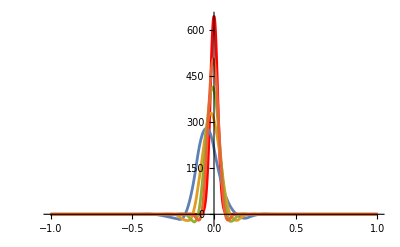

```mathematica
Show[exactPlot[d10],ListLinePlot[crossSectionData[[1,1;;4]],PlotRange->All,InterpolationOrder->2]]
```

General::munfl: Exp[-1710.18] is too small to represent as a normalized machine number; precision may be lost.

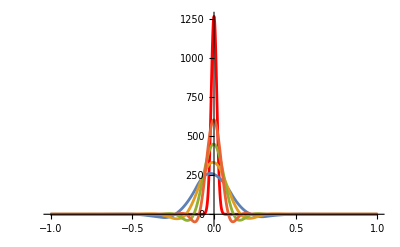

```mathematica
Show[exactPlot[d22],ListLinePlot[crossSectionData[[2,1;;4]],PlotRange->All,InterpolationOrder->2]]
```

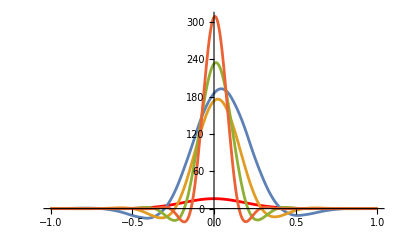

```mathematica
Show[exactPlot[d45],ListLinePlot[crossSectionData[[3,1;;4]],PlotRange->All,InterpolationOrder->2]]
```

```mathematica
yFixed
```

{0.1,0.05,0.025,0.0125}

```mathematica
yFixed=Table[First[yGrids[[j]]],{j,1,4}];
crossSections2=Table[midCol=Ns[[j]]/2;
dataAll[[i,j,midCol+1,All]],{i,1,3},{j,1,4}];

crossSectionData2=Table[yVals=Subdivide[-1.,1.,Length[crossSections2[[i,j]]]-1];
Transpose[{yVals,crossSections2[[i,j]]}],{i,1,3},{j,1,4}];
```

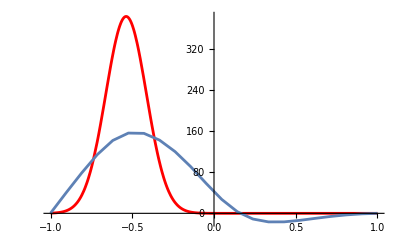

```mathematica
Show[exactPlot[0.1,d10],ListLinePlot[crossSectionData2[[1,1]],PlotRange->All]]
```

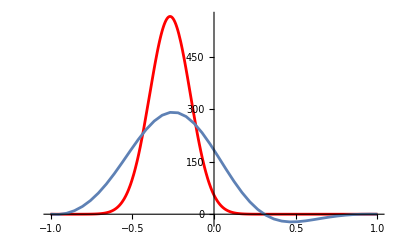

```mathematica
Show[exactPlot[0.05,d10],ListLinePlot[crossSectionData2[[1,2]],PlotRange->All]]
```

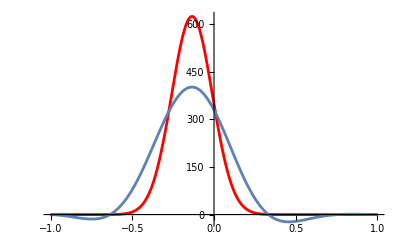

```mathematica
Show[exactPlot[0.025,d10],ListLinePlot[crossSectionData2[[1,3]],PlotRange->All]]
```

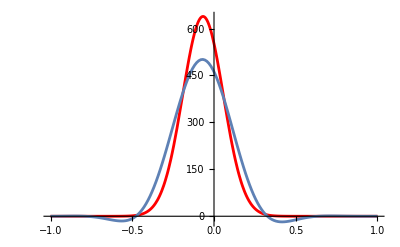

```mathematica
Show[exactPlot[0.0125,d10],ListLinePlot[crossSectionData2[[1,4]],PlotRange->All]]
```

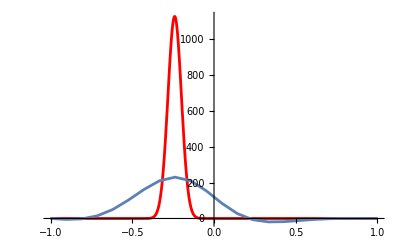

```mathematica
Show[exactPlot[0.1,d22],ListLinePlot[crossSectionData2[[2,1]],PlotRange->All]]
```

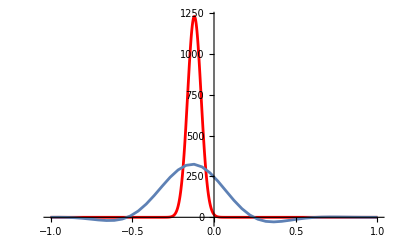

```mathematica
Show[exactPlot[0.05,d22],ListLinePlot[crossSectionData2[[2,2]],PlotRange->All]]
```

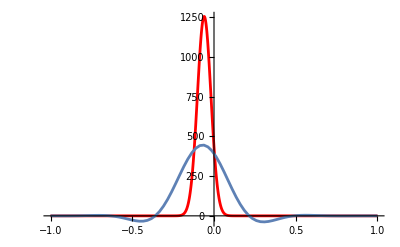

```mathematica
Show[exactPlot[0.025,d22],ListLinePlot[crossSectionData2[[2,3]],PlotRange->All]]
```

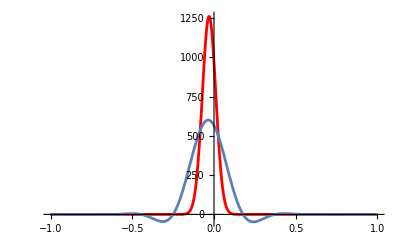

```mathematica
Show[exactPlot[0.0125,d22],ListLinePlot[crossSectionData2[[2,4]],PlotRange->All]]
```

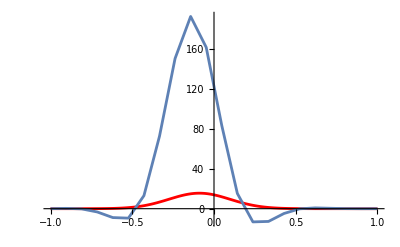

```mathematica
Show[exactPlot[0.1,d45],ListLinePlot[crossSectionData2[[3,1]],PlotRange->All]]
```

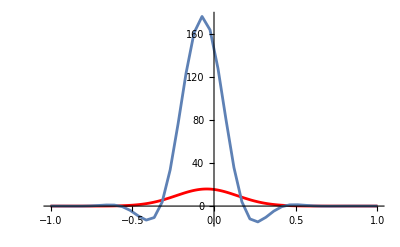

```mathematica
Show[exactPlot[0.05,d45],ListLinePlot[crossSectionData2[[3,2]],PlotRange->All]]
```

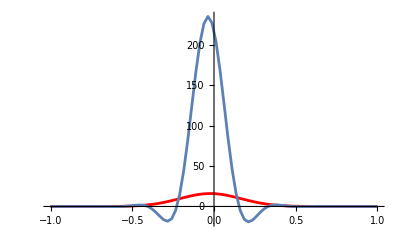

```mathematica
Show[exactPlot[0.025,d45],ListLinePlot[crossSectionData2[[3,3]],PlotRange->All]]
```

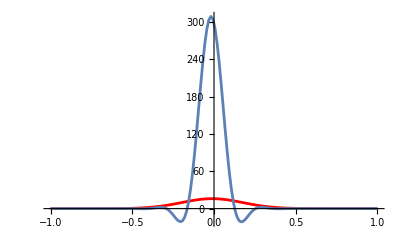

```mathematica
Show[exactPlot[0.0125,d45],ListLinePlot[crossSectionData2[[3,4]],PlotRange->All]]
```

```mathematica
data=Import["C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\anisotropic_N160_theta45\\final.csv"];
ListContourPlot[data,DataRange->{{-1,1},{-1,1}},PlotLegends->Automatic,PlotRange->All,Contours->15,ColorFunction->"Rainbow",ContourStyle->None]
```

-Graphics-

```mathematica
u[x_,y_,t_]:=1/(4*Pi*t*Det[d])*Exp[-(Transpose[{x,y}].Inverse[d].{x,y})/(4*t)];
```

```mathematica
ContourPlot[u[x,y,0.2,d45],{x,-1,1},{y,-1,1},PlotLegends->Automatic,PlotRange->All,Contours->20,ColorFunction->"Rainbow",ContourStyle->None]
```

-Graphics-